```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"-> "/Library/TeX/texbin/pdflatex"];
ConfigureMaTeX["Ghostscript"-> "/usr/local/bin/gs"];
teXBig=MaTeX[HoldForm[#],Magnification->1.75]&;
teXSmall=MaTeX[HoldForm[#],Magnification->1.25]&;
```

```mathematica
expr1=(Eγ^2((β βBar)^2-1)/. βBar-> √(1-(4 me^2)/(m★)^2)//Expand);
expr2=Eγ^2(((2 SubPlus[λ])/Eγ-1)^2-1)//Expand;
Normal@Series[Eγ/.Solve[expr1==expr2//Expand,Eγ]⟦1⟧/. me^2(m★)^2-> x/. me^2 SubPlus[λ]^2-> y,{me,0,6}];
Simplify[Series[%/. x-> me^2(m★)^2/. y-> me^2 SubPlus[λ]^2,{me,0,2}],{m★>0, SubPlus[λ]>0}]
plotExpr=Normal@%;
```

(2 (-1+√(β^2)) λ_+)/(-1+β^2)+(4 (-2 β^2+√(β^2) (1+β^2)) λ_+ me^2)/((m★)^2 (-1+β^2)^2)+O[me]^3

## Plot of RMC phase space

We are interested in  the RMC reaction 

μ  [A,Z] →  ν γ^* [A,Z-1]     with γ^*→ e^+e^-

Let us consider the virtual photon to have a mass of m_*, the positron to have energy E_+ (or Ep in the code), and the photon to have energy E_γ.

The energy of the positron is given as 

E_+  = γ_lab ℰ ( 1 + β_lab β_e cosϑ) = γ_lab  (m_*)/2(1+√(1-((m_*)/E_γ)^2)√(1-((4 m_e)/(_(m_*)))^2)cosϑ) =  1/2 E_γ (1+√(1-((m_*)/E_γ)^2)√(1-((4 m_e)/(_(m_*)))^2)cosϑ)

Let us take E_γas a fixed constant, the we can plot the envelope of available phase space in the

### (m_★)^(±) stuff

```mathematica
Ep=1/2 Eγ (1+ √(1-((m★)/Eγ)^2) √(1-((2me)/(m★))^2)cosϑ);
Solve[(Ep/. cosϑ-> 1)==λp,m★]//Simplify;
toPrint={%⟦2⟧,%⟦4⟧};
Clear[Ep];
toPrint=toPrint/.λp-> Ep
```

{{m★→√2 √(-Ep^2+Ep Eγ+me^2-√((Ep^2-me^2) (Ep^2-2 Ep Eγ+Eγ^2-me^2)))},{m★→√2 √(-Ep^2+Ep Eγ+me^2+√((Ep^2-me^2) (Ep^2-2 Ep Eγ+Eγ^2-me^2)))}}

```mathematica
FullSimplify[toPrint/. Ep-> Eγ (1-δ-ϵ)/. me-> Eγ ϵ ,Eγ>0]
```

{{m★→√2 Eγ √(ϵ-δ (-1+δ+2 ϵ)-√((-1+δ) δ (-1+δ+2 ϵ) (δ+2 ϵ)))},{m★→√2 Eγ √(ϵ-δ (-1+δ+2 ϵ)+√((-1+δ) δ (-1+δ+2 ϵ) (δ+2 ϵ)))}}

### Phase space plot

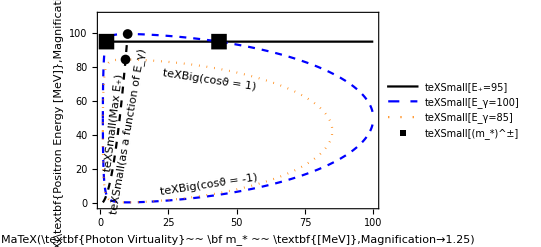

```mathematica
Ep=1/2 Eγ (1+ √(1-((m★)/Eγ)^2) √(1-((2me)/(m★))^2)cosϑ);

me= 0.511;
(* Plot maximum line *)
pMaxLine=ParametricPlot[ {√(2me Eγ),Ep/. m★-> √(2 me Eγ)/. cosϑ-> 1 },{Eγ,2me,100},PlotStyle->{Black,Dashed}];

Eγ= 100;
max1={m★,Ep/. cosϑ-> 1}/.m★-> √(2 me Eγ);
λp=95;


(* Get end intersection of curve with line*)
Solve[(Ep/. cosϑ-> 1)==λp,m★]//Simplify;
pointSub={%⟦3⟧,%⟦4⟧};
pL={m★,Ep/.cosϑ-> 1}/.pointSub⟦1⟧;
pR={m★,Ep/.cosϑ-> 1}/.pointSub⟦2⟧;
pLpR=ListPlot[{pL,pR},PlotMarkers-> Style["■",16],PlotStyle->{Black,PointSize[0.02]},PlotLegends->teXSmall/@{Style["(m_*)^±",16]}];


(* Plot flat line and  intersection of curve with line*)
pλp=Plot[{λp},{m★,1,Eγ},PlotLegends->LineLegend[teXSmall/@ {"E_+=95"},LegendMarkerSize->25], PlotRange->{0,110}, PlotStyle->{Black} ];
p95=Plot[{Ep/. cosϑ->- 1,Ep/. cosϑ-> 1},{m★,2me,Eγ},PlotLegends->LineLegend[teXSmall/@{"E_γ=100"},LegendMarkerSize->25],PlotStyle->{{Blue,Dashed}}];


Eγ= 85;
max2={m★,Ep/. cosϑ-> 1}/.m★-> √(2 me Eγ);
pMax=ListPlot[{max1,max2},PlotStyle->{Black,PointSize[0.02]},PlotMarkers->Style["●",10]];
p80=Plot[{Ep/. cosϑ->- 1,Ep/. cosϑ-> 1},{m★,2me,Eγ}, PlotLegends->LineLegend[teXSmall/@{"E_γ=85"},LegendMarkerSize->25],PlotStyle->{{Orange,Dotted}}];

img=Show[pλp,p95,p80,pMaxLine,pLpR,pMax,PlotRange-> {-1,110},Epilog->{Inset[Rotate[teXBig@"cosϑ = -1",0.15],{40,11}],Inset[Rotate[teXBig@"cosϑ = 1",-0.15],{40,72.5}],
Inset[Rotate[teXSmall@"Max E_+",1.45],{5,47.5}],
Inset[Rotate[teXSmall@HoldForm@"as a function of E_γ",1.4],{10.27,42.5}]},Axes-> True,FrameStyle-> Black,Frame-> True,FrameLabel->(MaTeX[#,Magnification->1.25]&)/@ {"\\textbf{Photon Virtuality}~~ \\bf m_* ~~  \\textbf{[MeV]}", "\\textbf{Positron Energy   [MeV]}"},PlotRangePadding-> 0,FrameTicks-> Automatic]
Clear[me,Eγ,λp]
```

```mathematica
Export["~/Desktop/phase-space-plt.pdf",img]
```

~/Desktop/phase-space-plt.pdf

## Plot of near-end point phase space (zoomed in)

```mathematica
Ep/. m★-> √(2 me Eγ)/.Eγ-> 88/. cosϑ-> 1/. me-> 0.511
```

87.489

```mathematica
me= 0.511;

(* Plot maximum line *)
deltaBarL1=ParametricPlot[ {z,Ep/. m★-> √(2 me Eγ)/.Eγ-> 95/. cosϑ-> 1 },{z,√(2me 95),95},PlotStyle->{Black}];
deltaBarL2=ParametricPlot[ {85,-z+Ep/. m★-> √(2 me Eγ)/.Eγ-> 95/. cosϑ-> 1 },{z,0,2.1},PlotStyle->{Black}];
deltaBarL3=ParametricPlot[ {85,85+z },{z,0,4.2},PlotStyle->{Black}];
deltaL1=ParametricPlot[ { ( √(2 me Eγ)/.Eγ-> 92)+z,Ep/. m★-> √(2 me Eγ)/.Eγ-> 92/. cosϑ-> 1 },{z,-4,4},PlotStyle->{Black,Dashed}];
deltaL2=ParametricPlot[ {( √(2 me Eγ)/.Eγ-> 92),-z+Ep/. m★-> √(2 me Eγ)/.Eγ-> 92/. cosϑ-> 1 },{z,0,0.8},PlotStyle->{Black}];
deltaL3=ParametricPlot[ {( √(2 me Eγ)/.Eγ-> 92),88+z },{z,0,0.8},PlotStyle->{Black}];
Eγ= 95;
max1={m★,Ep/. cosϑ-> 1}/.m★-> √(2 me Eγ);
λp=85;


(* Get end intersection of curve with line*)
Solve[(Ep/. cosϑ-> 1)==λp,m★]//Simplify;
pointSub={%⟦3⟧,%⟦4⟧};
pL={m★,Ep/.cosϑ-> 1}/.pointSub⟦1⟧;
pR={m★,Ep/.cosϑ-> 1}/.pointSub⟦2⟧;
pLpR1=ListPlot[{pL,pR},PlotMarkers-> Style["■",16],PlotStyle->{Black,PointSize[0.02]},PlotLegends->{Style["(m_*)^±((λ̄)_+)",16]}];



(* Plot flat line and  intersection of curve with line*)
pλp=Plot[{λp},{m★,1,Eγ},PlotStyle->{Black}];
pEp=Plot[{88},{m★,1,Eγ},PlotStyle->{Black,Dashed}];
p95=Plot[{Ep/. cosϑ->- 1,Ep/. cosϑ-> 1},{m★,2me,Eγ},PlotStyle->Blue];


Eγ= 92;
max2={m★,Ep/. cosϑ-> 1}/.m★-> √(2 me Eγ);
p80=Plot[{Ep/. cosϑ->- 1,Ep/. cosϑ-> 1},{m★,2me,Eγ},PlotStyle->{Orange,Dashed}];

Solve[(Ep/. cosϑ-> 1)==88,m★]//Simplify;
pointSub={%⟦3⟧,%⟦4⟧};

pL={m★,Ep/.cosϑ-> 1}/.pointSub⟦1⟧;
pR={m★,Ep/.cosϑ-> 1}/.pointSub⟦2⟧;
pLpR2=ListPlot[{pL,pR},PlotMarkers->Style["●",12],PlotStyle->{Black,PointSize[0.02]},PlotLegends->{Style["(m_*)^±(E_+)",16]}];


Eγ= 95;
img=Show[pEp,pλp,p95,p80,deltaL1,deltaL2,deltaL3,deltaBarL1,deltaBarL2,deltaBarL3,pLpR2,pLpR1,PlotRange-> {75,95},Epilog->{Style[Text["E_+>(λ̄)_+",{65,89}],14,Black],Style[Text["δ̄",{85.4,90.9}],14,Black],Style[Text["δ",{9.7,89.62}],14,Black],Style[Text["Λ_+(m_*; E_γ=(Λ̄)_*)",{80.4,82.5}],16,Blue],Style[Text["Λ_+(m_*,E_γ<(Λ̄)_*)",{44,80.5}],16,Orange]},AxesStyle-> Black,Frame->True,FrameStyle-> Black,FrameLabel->(Style[#,16]&/@ {"m_*","E_+"})]
Clear[me,Eγ,λp]
```

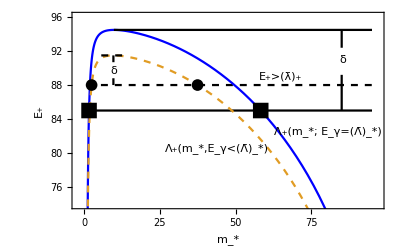

I have copy and pasted the point legends above onto the plot itself